## Steady-state isothermal vortex

```mathematica
1/r D[r p[r],r]==p[r]/r+(ρ[r] uϕ[r]^2)/r//Simplify
%/.p->Function[r,cs^2 ρ[r]]
%/.uϕ->Function[r,Ω[r]r]
%/.Ω->Function[r,Ω0 Exp[-r^2/(2 r0^2)]]
ρ[r]/.First@DSolve[%,ρ,r]//FullSimplify
```

p'[r]==(uϕ[r]^2 ρ[r])/r

cs^2 ρ'[r]==(uϕ[r]^2 ρ[r])/r

cs^2 ρ'[r]==r ρ[r] Ω[r]^2

cs^2 ρ'[r]==ⅇ^(-r^2/r0^2) r Ω0^2 ρ[r]

ⅇ^(-(ⅇ^(-r^2/r0^2) r0^2 Ω0^2)/(2 cs^2)) C[1]

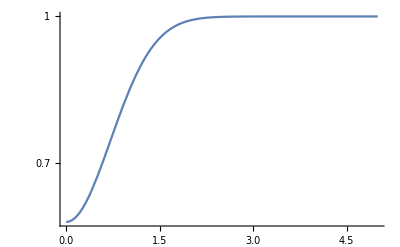

```mathematica
LogPlot[ⅇ^(-(ⅇ^(-r^2/r0^2) r0^2 Ω0^2)/(2 cs^2))/.{Ω0->1,cs->1,r0->1},{r,0,5},PlotRange->All]
```